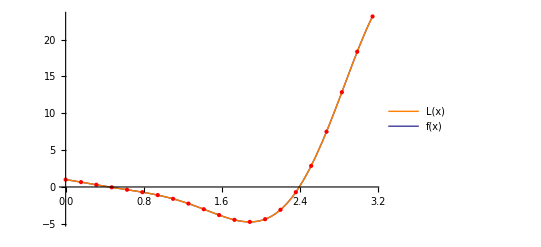

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0433671}. NIntegrate obtained 7.07436×10^-22 and 7.96573×10^-24 for the integral and error estimates.

Погрешность приближения для функции равна: 2.65977×10^-11

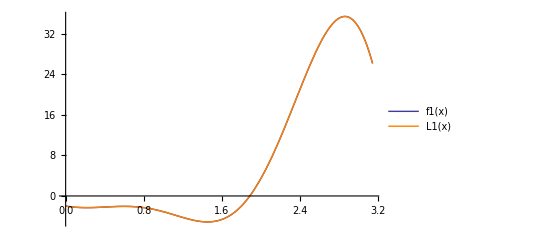

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0631806}. NIntegrate obtained 5.40098×10^-19 and 8.01657×10^-21 for the integral and error estimates.

Погрешность приближения для производной первого порядка функции равна: 7.34914×10^-10

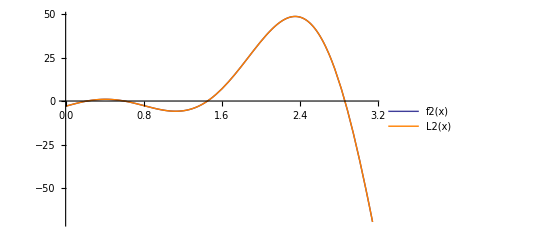

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0217285}. NIntegrate obtained 3.25066×10^-15 and 2.34519×10^-17 for the integral and error estimates.

Погрешность приближения для производной второго порядка функции равна: 5.70146×10^-8

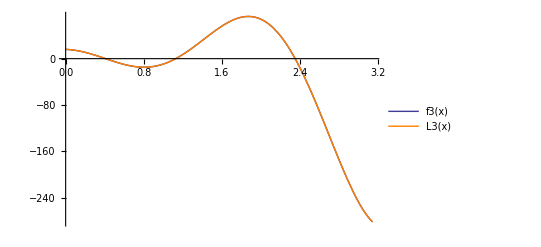

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0123472}. NIntegrate obtained 2.14095×10^-12 and 3.18337×10^-14 for the integral and error estimates.

Погрешность приближения для производной третьего порядка функции равна: 1.4632×10^-6

```mathematica
(*Зададим данную функцию*)
f[x_]=Exp[x]*Cos[2*x]-Sin[3*x];
(*Зададим отрезок*)
a=0;
b=Pi;
(*Построим график заданной функции на данном отрезке*)
G=Plot[f[x],{x,a,b},PlotRange->All,PlotLegends->"Expressions"];
(*Зададим количество частичных отрезков*)
n=20;
(*Зададим шаг разбиения*)
h=(b-a)/n;
(*Построим таблицу значений данной функции*)
X=Table[a+k*h,{k,0,n}];
Y=Table[f[X[[k]]],{k,1,n+1}];
XY=Table[{X[[k]],Y[[k]]},{k,1,n+1}];
(*Построим график таблично заданной функции*)
GP=ListPlot[XY,PlotStyle->Red,PlotRange->All,PlotLegends->"Expressions"];
(*Построим многочлен Лагранжа методами XVIII века*)L[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Построим график многочлена Лагранжа*)
GL=Plot[L[x],{x,a,b},PlotStyle->Orange,PlotRange->All,PlotLegends->"Expressions"];
(*Найдем производные многочлена Лагранжа до третьего порядка включительно и построим их графики*)
L1[x_]=D[L[x],x];
L2[x_]=D[L[x],{x,2}];
L3[x_]=D[L[x],{x,3}];
GL1=Plot[L1[x],{x,a,b},PlotStyle->Orange,PlotRange->All,PlotLegends->"Expressions"];
GL2=Plot[L2[x],{x,a,b},PlotStyle->Orange,PlotRange->All,PlotLegends->"Expressions"];
GL3=Plot[L3[x],{x,a,b},PlotStyle->Orange,PlotRange->All,PlotLegends->"Expressions"];
(*Найдем производные данной функции до третьего порядка включительно  и построим их графики*)
f1[x_]=D[f[x],x];
f2[x_]=D[f[x],{x,2}];
f3[x_]=D[f[x],{x,3}];
G1=Plot[f1[x],{x,a,b},PlotRange->All,PlotLegends->"Expressions"];
G2=Plot[f2[x],{x,a,b},PlotRange->All,PlotLegends->"Expressions"];
G3=Plot[f3[x],{x,a,b},PlotRange->All,PlotLegends->"Expressions"];
Show[G,GL,GP]
r=Sqrt[NIntegrate[(f[x]-L[x])^2,{x,a,b}]];
Print["Погрешность приближения для функции равна: ",r]
Show[G1,GL1]
r1=Sqrt[NIntegrate[(f1[x]-L1[x])^2,{x,a,b}]];
Print["Погрешность приближения для производной первого порядка функции равна: ",r1]
Show[G2,GL2]
r2=Sqrt[NIntegrate[(f2[x]-L2[x])^2,{x,a,b}]];
Print["Погрешность приближения для производной второго порядка функции равна: ",r2]
Show[G3,GL3]
r3=Sqrt[NIntegrate[(f3[x]-L3[x])^2,{x,a,b}]];
Print["Погрешность приближения для производной третьего порядка функции равна: ",r3]
```

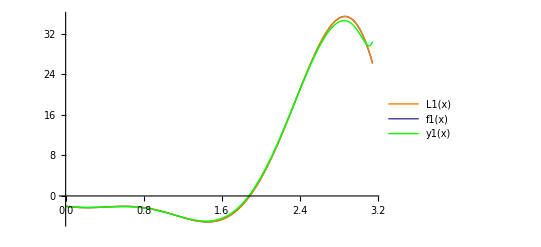

Погрешность приближения для разностной производной первого порядка функции равна: 0.774286

```mathematica
(*Построим таблицу значений производной данной функции, используя разностные производные*)
Y1=Table[0,{k,0,n}];
(*Найдем значение производной в левой точке, используя правую разностную производную*)
Y1[[1]]=(Y[[2]]-Y[[1]])/h;
(*Найдем значения производной во внутренних узлах, используя центральную разностную производную*)
For[k=2,k≤n,k++,
Y1[[k]]=(Y[[k+1]]-Y[[k-1]])/(2*h)
];
(*Найде значение производной в правой точке, используя левую разностную производную*)
Y1[[n+1]]=(Y[[n]]-Y[[n+1]])/(-h);
(*ВЫполним интерполяцию найденной производной*)y1[x_]=Sum[Y1[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
GY1=Plot[y1[x],{x,a,b},PlotRange->All,PlotStyle->Green,PlotLegends->"Expressions"];
Show[G1,GL1,GY1]
ry1=Sqrt[NIntegrate[(f1[x]-y1[x])^2,{x,a,b}]];
Print["Погрешность приближения для разностной производной первого порядка функции равна: ",ry1]
```